## Да се намери приближено стойността на sin ¶/5, като се използва интерполационният полином на Лагранж с възли 0, ¶/6, ¶/3 и ¶/2 и да се даде оценка на грешката при тази апроксимация.

```mathematica
(*Построяваме интерполационния полином на Лагранж*)
l0[x_]=((x-Pi/6)(x-Pi/3)(x-Pi/2))/((0-Pi/6)(0-Pi/3)(0-Pi/2));
l1[x_]=((x-0)(x-Pi/3)(x-Pi/2))/((Pi/6-0)(Pi/6-Pi/3)(Pi/6-Pi/2));
l2[x_]=((x-0)(x-Pi/6)(x-Pi/2))/((Pi/3-0)(Pi/3-Pi/6)(Pi/3-Pi/2));
l3[x_]=((x-0)(x-Pi/6)(x-Pi/3))/((Pi/2-0)(Pi/2-Pi/6)(Pi/2-Pi/3));
p[x_]=N[Expand[l0[x]*0+l1[x]*1/2+l2[x]*(√3)/2+l3[x]*1]]
```

1.02043 x-0.0654708 x^2-0.113872 x^3

```mathematica
p[Pi/5] (*Приближената стойност на sin (Pi/5)*)
```

0.587061

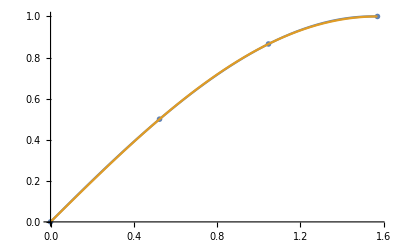

```mathematica
plot1=ListPlot[{{0,0},{Pi/6,1/2},{Pi/3,√3/2},{Pi/2,1}},PlotMarkers->●];
plot2=Plot[{p[x],Sin[x]},{x,0,Pi/2}];
Show[plot1,plot2]
(*При интерполация приближението е доста добро*)
```

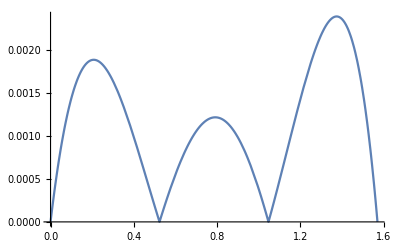

```mathematica
Plot[Abs[p[x]-Sin[x]],{x,0,Pi/2}] (*графика на модула на абсолютната грешка*)
```

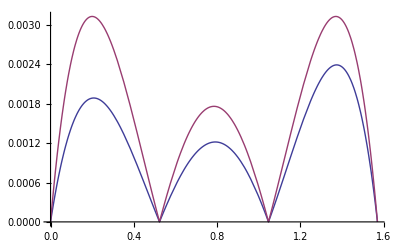

```mathematica
Plot[{Abs[p[x]-Sin[x]],1/24 Abs[(x-0)(x-Pi/6)(x-Pi/3)(x-Pi/2)]},{x,0,Pi/2}](*Действителната грешка никъде не надминава изведената оценка*)
```

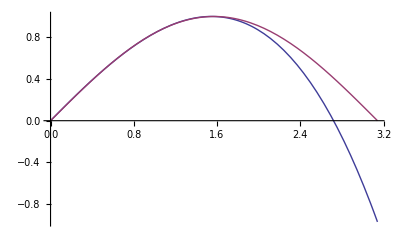

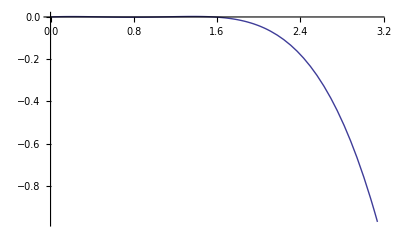

```mathematica
Plot[{p[x],Sin[x]},{x,0,Pi}]
Plot[p[x]-Sin[x],{x,0,Pi}]  (*При екстраполация не можем да разчитаме на добро приближение*)
```

## Начертайте графиките на базисните полиноми на Лагранж.

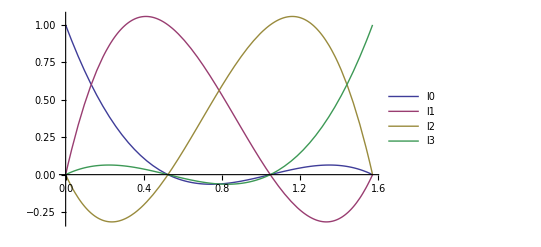

```mathematica
Plot[{l0[x],l1[x],l2[x],l3[x]},{x,0,Pi/2},PlotLegends->{"l0","l1","l2","l3"}]
```